The number of pixels and the FFOV are limited by the laser repetition rate, i.e., how many laser pulses fit in a scanned line.
For a 80 MHz laser and 8 kHz scanner, there are 80 MHz/(2*8 kHz) = 5000 pulses. For example, if we have 10 pulses per pixel, then there could be 500 pixels max

```mathematica
μm = 10^-6;
μs=10^-6;
ms=10^-3;
ns = 10^-9;
mm=10^-3;
kHz=10^3;
Tline=62.5μs;(*Time per scanned line*)
Tlaser = 12.5ns;(*Laser pulse repetition period*)
tFPGA = 6.25ns;(*FPGA clock*)
Δx=0.5μm;(*Spatial resolution*)

MaxPulsesPerPixel = 13;
dwell = MaxPulsesPerPixel *Tlaser ;
NpixFFOV=300;(*Effective pixel number. Even number*)
γ = Sin[π/2(NpixFFOV*dwell)/Tline];(*Spatial fill factor*)
FFOV=NpixFFOV * Δx ;(*Full field of view of the microscope)*)
FullScan= FFOV/γ  ;(*Full scan of the RS = distance between turning points*)
```

```mathematica
Grid[{{"Max pulses per pixel",13},{"Pixel dwell time (ns)",dwell/ns},{"Number of pixels",NpixFFOV},{"Fill factor",γ },{"Full scan(μm)",FullScan/μm},{"Full FOV (μm)",FFOV/μm}},Frame->All]
```

Max pulses per pixel | 13
Pixel dwell time (ns) | 162.5
Number of pixels | 300
Fill factor | 0.940881
Full scan(μm) | 159.425
Full FOV (μm) | 150.

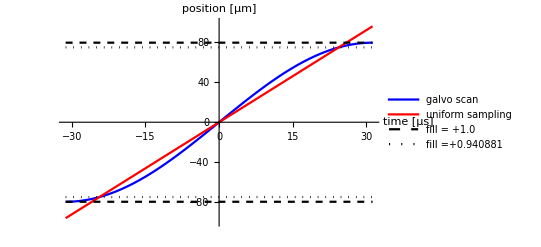

```mathematica
RSposition[t_]:=FullScan/2 Sin[π/Tline t](*Position of the resonant scanner vs time*)
time[x_]:=Tline/π ArcSin[2/FullScan x](*Convert from spatial coordinate to time*)
Plot[{RSposition[t μs]/μm,(FFOV/2)/time[FFOV/2] t μs/μm,{FullScan/2,-FullScan/2}/μm,{-FFOV/2,FFOV/2}/μm },{t,-Tline/2/μs,Tline/2/μs},PlotRange->{-100,100},PlotStyle->{Blue,Red,{Dashed,Black},{Dotted,Black}},AxesLabel->{"time [μs]","position [μm]"} , PlotLegends->{"galvo scan","uniform sampling","fill = +1.0","fill =" +γ}]
```

```mathematica
DiscreteTime[pix_]:=pix * dwell;(*Time discretization*)
DiscretePosition[pix_]:=RSposition[DiscreteTime[pix]](*Spatial discretization mapped from the time discretization*)

(*Tabulate the position vs time*)
NpixFullScan= Round[NpixFFOV/(2γ)]*2;(*Full pixel number. Divide and mulpliy by 2 to get an even number*)
header={"pixel","Time [μs]","Position [μm]"};
TableForm[Prepend[Table[{pix,DiscreteTime[pix]/μs,DiscretePosition[pix]/μm},{pix,NpixFullScan/2,0,-1}],header]]
```

pixel | Time [μs] | Position [μm]
159 | 25.8375 | 76.7806
158 | 25.675 | 76.6031
157 | 25.5125 | 76.4205
156 | 25.35 | 76.2327
155 | 25.1875 | 76.0399
154 | 25.025 | 75.842
153 | 24.8625 | 75.6391
152 | 24.7 | 75.4311
151 | 24.5375 | 75.218
150 | 24.375 | 75.
149 | 24.2125 | 74.7769
148 | 24.05 | 74.5489
147 | 23.8875 | 74.3159
146 | 23.725 | 74.0779
145 | 23.5625 | 73.835
144 | 23.4 | 73.5872
143 | 23.2375 | 73.3344
142 | 23.075 | 73.0768
141 | 22.9125 | 72.8142
140 | 22.75 | 72.5469
139 | 22.5875 | 72.2746
138 | 22.425 | 71.9976
137 | 22.2625 | 71.7158
136 | 22.1 | 71.4291
135 | 21.9375 | 71.1377
134 | 21.775 | 70.8416
133 | 21.6125 | 70.5407
132 | 21.45 | 70.2352
131 | 21.2875 | 69.9249
130 | 21.125 | 69.61
129 | 20.9625 | 69.2904
128 | 20.8 | 68.9662
127 | 20.6375 | 68.6374
126 | 20.475 | 68.304
125 | 20.3125 | 67.9661
124 | 20.15 | 67.6237
123 | 19.9875 | 67.2767
122 | 19.825 | 66.9252
121 | 19.6625 | 66.5693
120 | 19.5 | 66.2089
119 | 19.3375 | 65.8441
118 | 19.175 | 65.4749
117 | 19.0125 | 65.1014
116 | 18.85 | 64.7235
115 | 18.6875 | 64.3413
114 | 18.525 | 63.9548
113 | 18.3625 | 63.564
112 | 18.2 | 63.169
111 | 18.0375 | 62.7698
110 | 17.875 | 62.3664
109 | 17.7125 | 61.9588
108 | 17.55 | 61.5471
107 | 17.3875 | 61.1313
106 | 17.225 | 60.7114
105 | 17.0625 | 60.2874
104 | 16.9 | 59.8595
103 | 16.7375 | 59.4275
102 | 16.575 | 58.9916
101 | 16.4125 | 58.5517
100 | 16.25 | 58.1079
99 | 16.0875 | 57.6603
98 | 15.925 | 57.2088
97 | 15.7625 | 56.7535
96 | 15.6 | 56.2944
95 | 15.4375 | 55.8316
94 | 15.275 | 55.365
93 | 15.1125 | 54.8947
92 | 14.95 | 54.4208
91 | 14.7875 | 53.9432
90 | 14.625 | 53.4621
89 | 14.4625 | 52.9773
88 | 14.3 | 52.4891
87 | 14.1375 | 51.9973
86 | 13.975 | 51.5021
85 | 13.8125 | 51.0034
84 | 13.65 | 50.5013
83 | 13.4875 | 49.9959
82 | 13.325 | 49.4871
81 | 13.1625 | 48.975
80 | 13. | 48.4597
79 | 12.8375 | 47.9411
78 | 12.675 | 47.4193
77 | 12.5125 | 46.8944
76 | 12.35 | 46.3663
75 | 12.1875 | 45.8351
74 | 12.025 | 45.3009
73 | 11.8625 | 44.7637
72 | 11.7 | 44.2234
71 | 11.5375 | 43.6802
70 | 11.375 | 43.1342
69 | 11.2125 | 42.5852
68 | 11.05 | 42.0334
67 | 10.8875 | 41.4787
66 | 10.725 | 40.9214
65 | 10.5625 | 40.3612
64 | 10.4 | 39.7984
63 | 10.2375 | 39.233
62 | 10.075 | 38.6649
61 | 9.9125 | 38.0942
60 | 9.75 | 37.521
59 | 9.5875 | 36.9453
58 | 9.425 | 36.3671
57 | 9.2625 | 35.7865
56 | 9.1 | 35.2035
55 | 8.9375 | 34.6182
54 | 8.775 | 34.0306
53 | 8.6125 | 33.4406
52 | 8.45 | 32.8485
51 | 8.2875 | 32.2542
50 | 8.125 | 31.6577
49 | 7.9625 | 31.0591
48 | 7.8 | 30.4584
47 | 7.6375 | 29.8557
46 | 7.475 | 29.251
45 | 7.3125 | 28.6443
44 | 7.15 | 28.0358
43 | 6.9875 | 27.4253
42 | 6.825 | 26.8131
41 | 6.6625 | 26.199
40 | 6.5 | 25.5832
39 | 6.3375 | 24.9657
38 | 6.175 | 24.3466
37 | 6.0125 | 23.7258
36 | 5.85 | 23.1034
35 | 5.6875 | 22.4795
34 | 5.525 | 21.854
33 | 5.3625 | 21.2272
32 | 5.2 | 20.5989
31 | 5.0375 | 19.9692
30 | 4.875 | 19.3382
29 | 4.7125 | 18.7059
28 | 4.55 | 18.0724
27 | 4.3875 | 17.4376
26 | 4.225 | 16.8017
25 | 4.0625 | 16.1647
24 | 3.9 | 15.5266
23 | 3.7375 | 14.8874
22 | 3.575 | 14.2473
21 | 3.4125 | 13.6062
20 | 3.25 | 12.9642
19 | 3.0875 | 12.3214
18 | 2.925 | 11.6777
17 | 2.7625 | 11.0332
16 | 2.6 | 10.388
15 | 2.4375 | 9.74213
14 | 2.275 | 9.09559
13 | 2.1125 | 8.44845
12 | 1.95 | 7.80073
11 | 1.7875 | 7.1525
10 | 1.625 | 6.5038
9 | 1.4625 | 5.85465
8 | 1.3 | 5.20512
7 | 1.1375 | 4.55524
6 | 0.975 | 3.90506
5 | 0.8125 | 3.25461
4 | 0.65 | 2.60395
3 | 0.4875 | 1.95311
2 | 0.325 | 1.30215
1 | 0.1625 | 0.651096
0 | 0. | 0.